## To Do & Notes

不仅仅只对限定的四类Type信息处理。

[Done] 对于exponential的，输出中带有科学计数法的话处理 -> 用一个Interpreter替代ToExpression  Interpreter["Number"]["4.35456e-09"]
4.35456×10^-9

...

## Global Path Configure

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Network Project/compareFS_v0.1/NDN-EB-algo

## Read in Data

```mathematica
fileName = "gridcbr/100,2_sqrt(2)-best-expbf-nocs-rate-trace.txt";
(*分析grid-topo*)
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
n = Length[data]
data2 = Table[StringSplit[row,"\t"],{row,data}];
head = data2⟦1⟧;
entries = data2⟦2;;n⟧;
head
entries⟦1;;5⟧
```

26825

{Time,Node,FaceId,FaceDescr,Type,Packets,Kilobytes,PacketRaw,KilobytesRaw}

{{0.5,0,256,netDeviceFace://,InInterests,0,0,0,0},{0.5,0,256,netDeviceFace://,OutInterests,5115.2,0,3197,0},{0.5,0,256,netDeviceFace://,InData,68.8,71.125,43,44.4531},{0.5,0,256,netDeviceFace://,OutData,0,0,0,0},{0.5,0,256,netDeviceFace://,InSatisfiedInterests,0,0,0,0}}

## Data Preprocessing

```mathematica
(*0号节点对应consumer*)
consumerEntries = Select[entries,StringMatchQ[#⟦2⟧,"0"] &];
(*找到根据节点id把consumer节点分类，本topo中因为只有一个consumer所以差别不大，但是考虑到后面代码的兼容性，还是加这一行*)
consumer = GatherBy[consumerEntries,#⟦2⟧&];
consumer
```

{{{0.5,0,256,netDeviceFace://,InInterests,0,0,0,0},{0.5,0,256,netDeviceFace://,OutInterests,5115.2,0,3197,0},{0.5,0,256,netDeviceFace://,InData,68.8,71.125,43,44.4531},3088,{59.5,0,258,appFace://,OutTimedOutInterests,0,0,0,0},{59.5,0,-1,all,SatisfiedInterests,118,0,59,0},{59.5,0,-1,all,TimedOutInterests,9881.59,0,4941,0}}}
 |  |  |  |

```mathematica
(*找出consumer节点集合中第一个consumer，读出其中Type为一下四类的entries*) 
tmp = Table[Select[consumer⟦1⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&],
{t,{"InInterests","InData","OutInterests","OutData"}}];
(*读出符合条件的entires中的times和Kilobytes信息*)
times = Table[Interpreter["Number"][ele⟦1⟧],{ele,tmp⟦1⟧}];
inInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦1⟧}];
inData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦2⟧}];
outInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦3⟧}];
outData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦4⟧}];
(*对多个不同的Type处理*)
(*把time和Kilboytes关联起来，然后把相同times下的list聚集起来*)
n = Length[times];
test = Table[
GatherBy[Table[{times⟦i⟧, t⟦i⟧},{i,1,n}],First],
{t,{inInterests,inData,outInterests,outData}}
];
(*形成时间序列数据*)
(*TimeSeries的好处是方便用ML的技巧拟合模型*)
tsdata= Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,test⟦i⟧}
],{i,1,4}
];
```

```mathematica
Length[tsdata⟦2⟧]
```

119

## Visualization

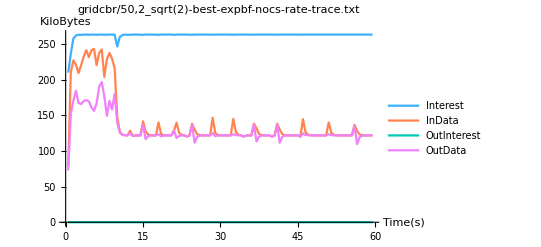

```mathematica
(*四个属性全部画在一起，会发现InInterest和OutInterest完全重合, InData和OutData全部重合，所以看上去只有二根线*)
ListPlot[{
TimeSeries[tsdata⟦1⟧],
TimeSeries[tsdata⟦2⟧],
TimeSeries[tsdata⟦3⟧],
TimeSeries[tsdata⟦4⟧]
},
PlotLabel-> fileName,
AxesLabel->{"Time(s)","KiloBytes"},
PlotLegends->{"Interest","InData","OutInterest","OutData"},
PlotStyle->96,
Joined->True
]
```

## Output Files for External Plotting

```mathematica
(*tmp1 = tsdata⟦2⟧;
tmp2 = tsdata⟦3⟧;
time = Table[node⟦1⟧,{node,tmp1}];
indata = Table[node⟦2⟧,{node,tmp1}];
outInterests = Table[node⟦2⟧,{node,tmp2}];*)
```

```mathematica
(*test = {time,indata,outInterests};
Export["fixWithoutCS.csv",test]*)
```